## Bayesian Statistics, Assignment for Friday, Sept. 27

## Starting our Bayes Book

It is time to review all we have read in Young (to the end of Section 11, p. 86). Is there anything you still want to discuss?

Next, it is finally time to open our Bayesian statistics book:

It starts off easy, but in a few more weeks, when we get to p. 87, you will be grateful that we spent Weeks 1-5 of Term 2 studying Young.

Study Chapter 1 of our Bayesian statistics book.

Bring questions about Chapter 1.

## For Problem Set 7

### Linear Regression

1. In Tuesday’s class, we had a water pressure example. The assumption was that the water pressure is rising linearly, perhaps because a tank is being steadily filled. We assume that water pressure actually obeys:

p(t)=a·t+b

After a great deal of algebra, and one potentially very wrong assumption, we found that the most probable values of a and b  are given by:

a=(M_bb M_a-M_ab M_b)/(M_aa M_bb-M_ab^2)     and      b=(M_aa M_b-M_ab M_a)/(M_aa M_bb-M_ab^2)

where

M_aa=∑_(i=1)^N t_i^2
M_ab=∑_(i=1)^N t_i
M_bb=∑_(i=1)^N 1=N
M_a=∑_(i=1)^N p_i t_i
M_b=∑_(i=1)^N p_i

This is colloquially known as the “best fit.” It is more precisely known as “least-squares fitting.”

(a) In class, our specific example had three pressure measurements:

59 psi at 15 minutes
61.5 psi at 25 minutes
63.5 psi at 35 minutes

Let’s subtract 59 psi from each pressure measurement. Let’s also not carry the units around. Then

t_1=15          p_1=0
t_1=25          p_2=2.5
t_1=35          p_3=4.5

With those values, what are the six M’s? (I filled in two of them for you below.)

M_aa=∑_(i=1)^N t_i^2= 2075
M_ab=∑_(i=1)^N t_i =
M_bb=∑_(i=1)^N 1=N = 3
M_a=∑_(i=1)^N p_i t_i =
M_b=∑_(i=1)^N p_i =

(b) Use  what you got for the M’s to get values for a and b.

a=(M_bb M_a-M_ab M_b)/(M_aa M_bb-M_ab^2)=

b=(M_aa M_b-M_ab M_a)/(M_aa M_bb-M_ab^2)=

(c) Graph the three data points on this graph:

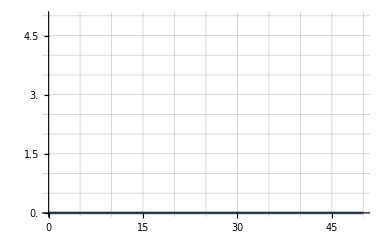

```mathematica
Plot[0, {t, 0, 50}, PlotRange->{{0, 50},{0,5}}, Ticks->{Range[0,50, 5],Range[0, 5, 0.5]},GridLines->{Range[0,50, 5],Range[0, 5, 0.5]}]
```

(d) Now, graph the straight line p=a·t+b on the graph above.

THOSE OF YOU WHO HAVE BEEN FREE-HANDING THINGS. IT’S TIME TO RAISE YOUR GAME. GET A RULER AND DO AN ACCURATE JOB OF PLACING THE SLOPE AND THE INTERCEPT.

(e) The three t_i values are 15, 25, and 35. You can plug those back in to p=a·t+b to get predicted values for p_1, p_2, and p_3.

Make a table with four columns and three rows. The four columns will be t_i, the measured pressure, p_(i, measured), the predicted pressure, p_(i, predicted), and the difference, d_i=p_(i, measured) - p_(i, predicted). Fill in the table. Leave some space for an extra column that you will put in in the next problem.

### χ^2

2. For a set of measurements each of which has uncertainty given by a standard deviation σ, the χ^2 of the set of measurements is defined to be

χ^2=∑_(i=1)^N d_i^2/σ^2

(a) In the example of Problem 1, we don’t know the σ for our measurements (I can explain why in class, but trust me, we don’t).  So let’s just assume, to make our lives simple, that σ=1. In that case the χ^2 is just the sum of the d_i^2. Add a column to the table you made in Problem 1(e) that is d_i^2.

(b) Total the new column up to get the χ^2 for the best fit to our data:

χ^2=∑_(i=1)^N d_i^2/σ^2=∑_(i=1)^N d_i^2/1^2=∑_(i=1)^N d_i^2=

### The Harvester, False Positives, and False Negatives

2. A village grows potatoes. The village is quite hungry, and they don’t want to lose any potatoes during harvest. They have a harvester that sorts the rocks and the potatoes, and if the harvester is set to lose only 5% of the potatoes, it unfortunately includes 20% of the rocks rocks.

(a) Let’s call a rock or a potato a “nodule.” Let’s say there are 9x as many rocks as potatoes in the field. If 1000 nodules go into the harvester, how many rocks go into the harvester, and how many potatoes go into the harvester?


(b) Let’s say the harvester gets 95% of the potatoes. Starting with the numbers in (a), how many potatoes were successfully collected by the harvester? How many potatoes were wasted?


(c) Still starting with the numbers from (a), let’s say that to get 95% of the potatoes, that unfortunately the harvester also collects 20% of the rocks. How many rocks were accidentally collected? How many rocks were successfully rejected?



(d) The successfully-harvested potatoes arrive at the village kitchen along with the accidentally-collected rocks. What percentage of the nodules delivered to the kitchen are potatoes. What percentage are rocks? What is the ratio of rocks to potatoes?